```mathematica
Clear[dist,list]
```

```mathematica
list[upleft_,downleft_,upright_,downright_]:=Module[{},Join[Transpose[Join[{Range[1,25]},{RandomSample[Join[Table[RandomInteger[{1,37}],upleft],Table[RandomInteger[{38,50}],downleft]]]}]],Transpose[Join[{Range[26,50]},{RandomSample[Join[Table[RandomInteger[{1,37}],upright],Table[RandomInteger[{38,50}],downright]]]}]]]]
```

```mathematica
dist[diagonal_]:=dist[diagonal]=Table[Module[{x=RandomInteger[{1,diagonal}]},list[x,25-x,25-(diagonal-x),diagonal-x]],5000]
```

```mathematica
dist[20][[1]]
```

{{1,49},{2,46},{3,42},{4,39},{5,31},{6,39},{7,48},{8,34},{9,28},{10,43},{11,43},{12,43},{13,48},{14,50},{15,49},{16,13},{17,42},{18,39},{19,39},{20,40},{21,7},{22,41},{23,44},{24,38},{25,41},{26,38},{27,49},{28,45},{29,23},{30,34},{31,45},{32,44},{33,41},{34,31},{35,42},{36,36},{37,41},{38,42},{39,5},{40,40},{41,43},{42,48},{43,5},{44,15},{45,45},{46,26},{47,41},{48,13},{49,12},{50,46}}

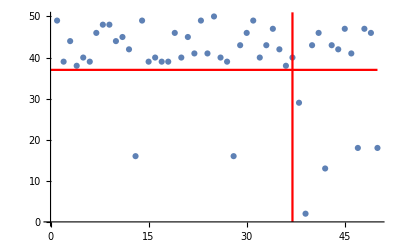

```mathematica
Show[ListPlot[dist[20][[3]]],ListLinePlot[Table[{37,x},{x,Range[0,51,0.01]}],PlotStyle->Red],ListLinePlot[Table[{x,37},{x,Range[0,50,0.01]}],PlotStyle->Red]]
```

# Leads connected to 1 - 10 and 41 to 50

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_,m_]:= t*IdentityMatrix[m]
```

```mathematica
Clear[T]
```

```mathematica
T[t_,m_]:=Module[{MAT=0*IdentityMatrix[m]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardul/PhD_new/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,2.49,0.01]}]
```

```mathematica
leads[50]
```

{1}
 |  |  |  |

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+1]]](*Module[{J=Inverse[β[ω,0.0001,1,0,m]],A:=Inverse[β[ω,0.0001,1,0,m]],Tx:=T1[1,m]},Do[J=Inverse[IdentityMatrix[m]-A.Tx.J.Tx].A,50000];J=J]*)
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
Clear[SLLEAD,SRLEAD]
```

```mathematica
SLLEAD[ω_,ml_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;ml,1;;ml]]=LEFT[ω,ml];MAT]
```

```mathematica
SRLEAD[ω_,mr_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;mr,1;;mr]]=LEFT[ω,mr];MAT]
```

```mathematica
device1[ω_,ml_,m_]:=Module[{},Inverse[IdentityMatrix[m]-g[ω,0.0001,1,0].T[1,m].SLLEAD[ω,ml].T[1,m]].g[ω,0.0001,1,0]]
```

```mathematica
TLD[t_,mr_]:=Module[{},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,mr}]->t]]]
```

```mathematica
CA[ω_,m_,ml_,mr_,ϵ1_,diagonal_,number_]:= Module[{},
recurs=Module[{J= device1[ω,ml,m]},
Do[
J=Inverse[IdentityMatrix[m]-Inverse[Module[{κ=β[ω,0.0001,1,0,m],n= dist[diagonal][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]].T1[1,m].J.T1[1,m]].Inverse[Module[{κ=β[ω,0.0001,1,0,m],n= dist[diagonal][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]],{loc1,50}];J=J];ir=Inverse[IdentityMatrix[m]-SRLEAD[ω,mr].TLD[1,mr].recurs.TLD[1,mr]].SRLEAD[ω,mr];il=Inverse[IdentityMatrix[m]-recurs.TLD[1,mr].SRLEAD[ω,mr].TLD[1,mr]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1,mr].recurs;
(*Gnonlocallr=recurs.ConjugateTranspose[TLD[1]].ir;*)
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1,mr].grr1.TLD[1,mr]-TLD[1,mr].GNON1.TLD[1,mr].GNON1]];TRA]
```

```mathematica
Mean[ParallelTable[CA[1,1,10,n],{n,2000}]]//AbsoluteTiming
```

{24.0583,3.3095}

```mathematica
ggg[diagonal_]:=Export["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_"<>ToString[diagonal]<>"_ϵ1_leads_41_50.dat",Table[{ω,Mean[ParallelTable[CA[ω,1,diagonal,NUM],{NUM,1000}]]},{ω,Range[-3,3,0.01]}]]
```

```mathematica
Table[Print[x];ggg[x],{x,Range[10,25,1]}]
```

{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_10_ϵ1_leads_41_50.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_11_ϵ1_leads_41_50.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_12_ϵ1_leads_41_50.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_13_ϵ1_leads_41_50.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_14_ϵ1_leads_41_50.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_15_ϵ1_leads_41_50.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_16_ϵ1_leads_41_50.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_17_ϵ1_leads_41_50.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_18_ϵ1_leads_41_50.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_19_ϵ1_leads_41_50.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_20_ϵ1_leads_41_50.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_21_ϵ1_leads_41_50.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_22_ϵ1_leads_41_50.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_23_ϵ1_leads_41_50.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_24_ϵ1_leads_41_50.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_25_ϵ1_leads_41_50.dat}

```mathematica
transmission = Table[{x,Import["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal1/50imp/3_4thon_left_diagonal_"<>ToString[x]<>"_ϵ1_leads_41_50.dat"]},{x,Range[10,25,1]}]
```

{{10,{{-3.,1.54421},{-2.99,1.68555},{-2.98,1.63706},{-2.97,1.52939},{-2.96,1.2798},{-2.95,1.33184},{-2.94,1.38944},{-2.93,1.3437},{-2.92,1.46788},{-2.91,1.1254},{-2.9,1.22407},{-2.89,1.49559},{-2.88,1.28537},576,{2.89,1.04732},{2.9,0.964516},{2.91,1.03412},{2.92,1.13449},{2.93,1.2205},{2.94,1.07412},{2.95,0.971659},{2.96,1.09924},{2.97,1.13853},{2.98,1.2345},{2.99,1.26483},{3.,1.2162}}},14,{25,{1}}}
 |  |  |  |

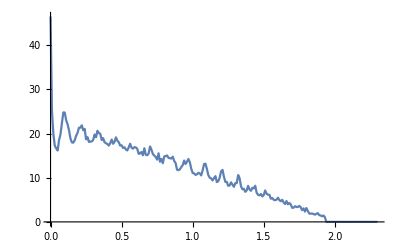

```mathematica
input=ParallelTable[{ω,CA[ω,50,50,50,0,10,1]},{ω,Range[0,2.3,0.01]}]//ListLinePlot
```

```mathematica
(*misfit16[n_,x_,y_]:=Module[{m5=Transpose[Join[{Range[-3,3,0.01]},{input[[n]]}]]},
ρ1:= Table[Module[{B1=Transpose[{m5[[1;;601]][[;;,1]],(m5[[1;;601,2]]-transmission[[ξ]][[1;;601,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{ξ,9}]; 
a1=Transpose[Join[{Range[10,90,10]},{ρ1}]];{a1,a1[[Position[a1,Min[a1]][[1,1]]]]}]*)
```

```mathematica
Dimensions[transmission]
```

{16,2}

```mathematica
misfit[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1=Table[{transmission[[con,1]],Module[{B1=Transpose[{m5[[1;;601]][[;;,1]],(m5[[1;;601,2]]-transmission[[con,2]][[1;;601,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)+NIntegrate[Interpolation[B1][ω],{ω,-3,-0.5}]/((2.5)*100)]},{con,16}];lista=ρ1(*,ρ2,ρ3,ρ4*)(*,ρ5,ρ6*);
{lista,lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

```mathematica
Mean[Table[Abs[misfit[3,0.5,n][[2]][[1]]-15]/15,{n,100}]]//N
```

0.236667

```mathematica
N[463/2000]
```

0.2315